```mathematica
Doc[k_]:=Labeled[allGraphs5[k,"graph"],k]->BaseGenerators2[allGraphs5[k,"colofour"]]
```

```mathematica
With[
{k=3036},
{Doc[k],
TableForm[
Table[
Doc[child]
,{child,allGraphs5[k,"parents"]}]
]}
]
```

{-Graphics-3036→<|2→{v123x45}|>,-Graphics-3033→<|2→{v123x45},3→{v12x35x4}|>
-Graphics-3027→<|2→{v123x45},3→{v12x34x5}|>
-Graphics-3009→<|2→{v123x45},3→{v13x25x4}|>
-Graphics-2955→<|2→{v123x45},3→{v13x24x5}|>
-Graphics-2307→<|2→{v123x45},3→{v15x23x4}|>
-Graphics-849→<|2→{v123x45},3→{v14x23x5}|>}

```mathematica
SymbolComp3[x_,y_]:=Block[{n1=SymbolName[x],n2=SymbolName[y]},
AlphabeticOrder[n1,n2]
]
```

```mathematica
Monitor[
Select[
Table[
{Labeled[allGraphs3[k,"graph"],k],
Fold[And,
Table[
With[
{p=Sort[First[BaseGenerators2[allGraphs3[k,"colofour"]]],SymbolComp3],
c=Sort[First[BaseGenerators2[allGraphs3[child[[2]],"colofour"]]],SymbolComp3]},
(c==Intersection[p,c])
]
,{child,allGraphs3[k,"children"]}]
]},
{k,Sort[Select[Keys[allGraphs3],allGraphs3[#,"children"]≠{}&]]}
]
,!#[[2]]&],
k]//Length
```

0

```mathematica
Monitor[
Select[
Table[
{Labeled[allGraphs4[k,"graph"],k],
Fold[And,
Table[
With[
{p=Sort[First[BaseGenerators2[allGraphs4[k,"colofour"]]],SymbolComp3],
c=Sort[First[BaseGenerators2[allGraphs4[child[[2]],"colofour"]]],SymbolComp3]},
(c==Intersection[p,c])
]
,{child,allGraphs4[k,"children"]}]
]},
{k,Sort[Select[Keys[allGraphs4],allGraphs4[#,"children"]≠{}&]]}
]
,!#[[2]]&],
k]//Length
```

12

```mathematica
Monitor[
Select[
Table[
{Labeled[allGraphs5[k,"graph"],k],
Fold[And,
Table[
With[
{p=Sort[First[BaseGenerators2[allGraphs5[k,"colofour"]]],SymbolComp3],
c=Sort[First[BaseGenerators2[allGraphs5[child[[2]],"colofour"]]],SymbolComp3]},
(c==Intersection[p,c])
]
,{child,allGraphs5[k,"children"]}]
]},
{k,Sort[Select[Keys[allGraphs5],allGraphs5[#,"children"]≠{}&]]}
]
,!#[[2]]&],
k]//Length
```

480

```mathematica
Sort[{v125x34,v124x35,v1235x4,v1234x5},String SymbolName[#1]>SymbolName[#2]&]
```

{v125x34,v124x35,v1235x4,v1234x5}

```mathematica
First[<|2->{v15x234,v14x235,v135x24,v134x25,v125x34,v124x35,v1235x4,v1234x5}|>]
```

{v15x234,v14x235,v135x24,v134x25,v125x34,v124x35,v1235x4,v1234x5}

```mathematica
Keys[allGraphs5[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
With[
{k=1},
{Doc[k],
TableForm[
Table[
{
Doc[child[[1]]],
Doc[child[[2]]]
}
,{child,allGraphs5[k,"children"]}]
]}
]
```

{-Graphics-1→<|2→{v15x234,v14x235,v135x24,v134x25,v125x34,v124x35,v1235x4,v1234x5}|>,-Graphics-19684→<|2→{v15x234,v14x235,v135x24,v134x25}|> | -Graphics-39367→<|2→{v125x34,v124x35,v1235x4,v1234x5}|>
-Graphics-6562→<|2→{v15x234,v14x235,v125x34,v124x35}|> | -Graphics-13123→<|2→{v135x24,v134x25,v1235x4,v1234x5}|>
-Graphics-2188→<|2→{v15x234,v135x24,v125x34,v1235x4}|> | -Graphics-5104→<|2→{v14x235,v134x25,v124x35,v1234x5}|>
-Graphics-730→<|2→{v14x235,v134x25,v124x35,v1234x5}|> | -Graphics-3646→<|2→{v15x234,v135x24,v125x34,v1235x4}|>
-Graphics-244→<|2→{v135x24,v134x25,v125x34,v124x35}|> | -Graphics-487→<|2→{v15x234,v14x235,v1235x4,v1234x5}|>
-Graphics-82→<|2→{v14x235,v134x25,v125x34,v1235x4}|> | -Graphics-190→<|2→{v15x234,v135x24,v124x35,v1234x5}|>
-Graphics-28→<|2→{v15x234,v135x24,v124x35,v1234x5}|> | -Graphics-136→<|2→{v14x235,v134x25,v125x34,v1235x4}|>
-Graphics-10→<|2→{v14x235,v135x24,v124x35,v1235x4}|> | -Graphics-22→<|2→{v15x234,v134x25,v125x34,v1234x5}|>
-Graphics-4→<|2→{v15x234,v134x25,v125x34,v1234x5}|> | -Graphics-16→<|2→{v14x235,v135x24,v124x35,v1235x4}|>}

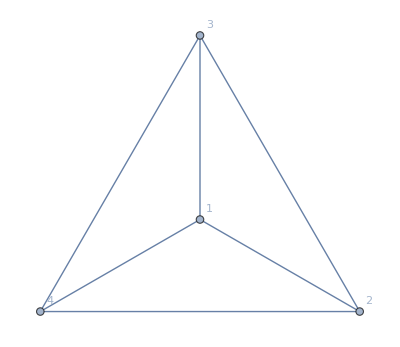

```mathematica
Graph[WheelGraph[4],VertexLabels->"Name"]
```

```mathematica
Monitor[
TableForm[
Table[
{k,
With[{s=BaseGenerators2[FindFullFormula[WheelGraph[k]]]},
Table[key->Length[s[key]],{key,Keys[s]}]
]},
{k,4,12}]
]
,k]
```